# C# Convertion to Mathematica Code

### Shortened height and new naming of code

```mathematica
c = 100; rep ={};
Do[(bm = k*2;cR=0;cC=2;dR=1;
While [(cR<bm-1),(
While [(cC<bm),(cR++;If [(cC ==(bm/2+1)),(cC=bm),(cC=(cC-1)*2+1)])];
If [(cC>bm),(cC=2*bm-cC+1;),(cC=2*(bm-cC+1);)];
If[(cC==2),(cR++;If[(cR<bm),dR++;])];
)];AppendTo[rep,dR];
),{k,1,c,1}];
Print[rep];
```

### ListPlot of 5000 values, A334672

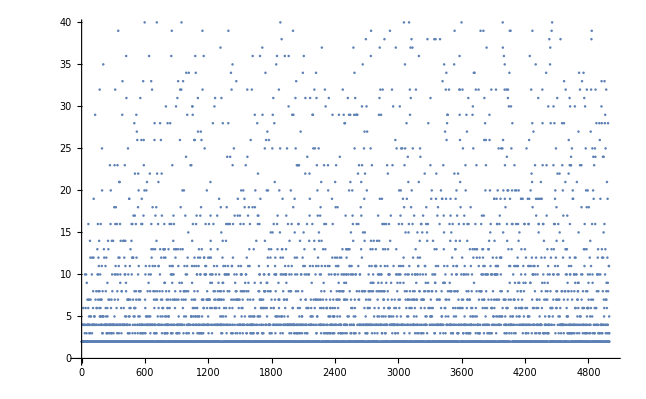

### Converted C# to Mathematica code, working raw

```mathematica
c = 50;
rep ={};
Do[
(
bm = k*2;
cR=0;
cC=2;
	didR=1;
While [
(cR<bm-1),
(While [(cC<bm),
(
cR++;
If [
(cC ==(bm/2+1)),
				(
		cC=bm
		),
		(
cC=(cC-1)*2+1
)
]
)];
If [
(cC>bm),
(
cC=2*bm-cC+1;
),
(
cC=2*(bm-cC+1);
)
];
If[
(cC==2),
(
cR++;
If[(cR<bm),
didR++;
]
)
];
)];
AppendTo[rep,didR];
),
{k,1,c,1}
];
Print[rep];
```

{2,2,2,2,2,2,2,4,2,2,4,2,4,2,2,6,2,2,2,2,2,2,4,2,4,2,2,2,2,3,4,10,2,2,2,2,2,6,4,2,2,2,10,2,2,2,3,2,9,2}

### ListPlot of 5000 values

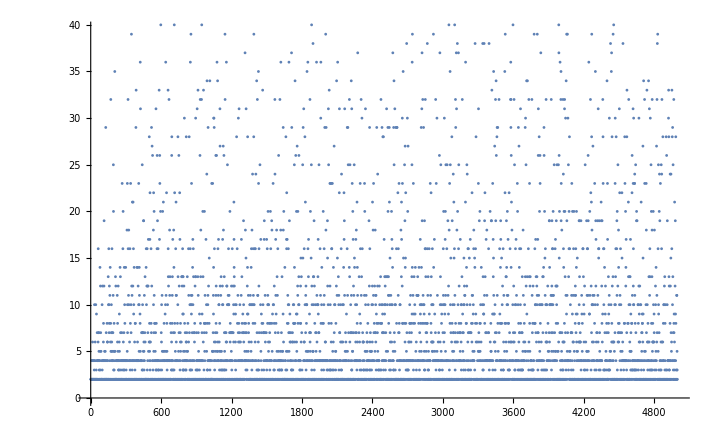

```mathematica
ListPlot[{2,2,2,2,2,2,2,4,2,2,4,2,4,2,2,6,2,2,2,2,2,2,4,2,4,2,2,2,2,3,4,10,2,2,2,2,2,6,4,2,2,2,10,2,2,2,3,2,9,2,2,2,2,4,7,4,2,4,2,2,2,4,6,16,4,2,7,2,7,5,4,3,4,2,2,2,4,2,14,2,3,5,12,2,7,2,2,5,2,2,4,2,2,2,2,2,10,3,2,12,4,2,4,2,2,2,4,6,8,4,2,2,12,19,4,2,2,5,2,2,4,2,2,5,4,2,2,29,2,2,2,7,4,2,2,2,2,2,8,4,2,6,6,2,4,2,2,2,13,2,10,2,2,16,2,10,7,8,12,2,4,2,11,2,2,14,2,6,2,8,32,5,4,2,7,10,2,5,6,2,16,4,7,5,4,2,4,2,7,4,11,2,25,20,3,2,2,5,8,3,5,2,4,2,35,2,2,5,2,2,13,2,2,12,2,2,4,4,2,2,2,2,4,2,4,11,2,6,8,4,2,5,4,12,4,3,2,2,2,3,4,2,6,9,5,2,4,2,2,14,3,2,13,7,2,52,4,2,4,2,2,2,4,2,7,2,3,23,4,2,4,2,2,16,4,20,4,6,4,2,2,3,7,2,3,14,4,2,10,4,8,2,2,2,4,4,2,14,2,4,4,3,2,2,2,2,4,2,18,4,5,23,10,7,2,2,4,32,16,2,2,11,2,18,10,2,2,4,2,2,6,4,2,16,4,3,4,8,2,23,2,2,10,7,2,2,39,2,12,4,2,11,3,4,21,4,2,2,12,2,21,2,2,16,4,9,10,4,2,14,2,2,4,6,2,2,3,2,8,8,2,2,2,4,29,2,33,4,2,2,4,2,2,14,4,2,2,4,6,14,4,2,4,12,2,2,4,10,23,2,4,5,10,14,11,2,2,2,2,9,8,36,5,31,4,2,4,2,2,2,4,4,7,2,2,4,2,3,25,2,7,10,3,7,7,2,2,5,2,19,19,4,6,5,3,2,11,4,2,2,7,2,13,6,2,2,2,2,2,2,2,14,16,2,10,2,2,12,2,2,16,3,2,12,4,2,7,2,12,2,17,5,55,2,2,2,2,6,28,4,8,5,6,17,22,3,2,2,6,2,4,94,2,16,8,2,7,29,2,12,2,2,27,2,2,2,26,2,4,4,3,2,2,18,10,22,5,2,7,20,11,2,2,8,4,2,2,8,4,5,4,2,7,2,2,31,3,3,8,2,2,4,4,57,16,26,2,2,19,4,4,4,2,16,3,3,4,2,2,2,2,2,33,2,2,17,4,26,23,57,3,2,2,2,20,4,40,2,2,2,7,2,6,10,3,2,4,11,2,5,4,2,20,2,2,2,2,5,21,4,2,2,2,4,8,2,4,5,2,4,2,4,2,9,2,2,10,2,36,2,5,11,4,2,2,22,4,2,8,5,3,4,4,2,10,4,2,2,33,16,13,2,12,4,2,2,32,4,2,4,2,18,11,4,2,13,2,2,8,2,2,2,106,2,7,4,3,4,6,26,28,4,3,8,11,13,4,4,17,2,2,3,7,2,2,2,18,2,14,3,2,40,2,7,22,8,2,4,2,2,5,2,2,16,4,2,21,11,6,11,4,2,4,2,2,41,4,2,8,2,2,10,28,13,100,4,2,5,2,2,26,7,2,12,2,2,4,22,2,17,3,4,7,6,8,5,2,2,77,2,2,6,45,2,13,2,2,13,12,2,4,2,16,9,13,3,13,3,9,5,4,2,53,12,3,2,2,30,4,8,2,5,4,4,7,2,2,2,2,3,4,3,6,28,4,6,4,4,7,5,4,2,13,2,2,5,2,8,70,2,2,2,16,6,11,4,2,2,28,2,7,47,2,2,10,3,4,16,36,4,3,2,10,39,2,11,2,9,23,10,3,2,11,4,7,4,2,14,2,17,10,2,2,16,2,13,4,2,49,7,4,2,7,6,2,8,2,2,12,2,2,13,2,30,13,2,3,100,2,2,7,4,4,76,3,2,31,4,4,2,2,3,13,33,2,11,7,2,5,4,66,2,2,4,4,3,9,2,2,2,26,2,32,4,8,2,13,18,2,4,2,2,4,32,2,40,4,7,9,2,2,2,4,53,20,4,13,2,6,2,33,2,2,121,3,2,7,8,20,8,5,2,4,11,2,2,2,2,8,2,2,17,2,2,7,10,2,5,24,2,34,2,3,8,2,3,4,10,11,29,2,2,4,12,2,2,4,2,8,15,2,4,82,4,34,3,2,4,2,2,4,4,2,171,2,2,2,2,2,2,23,2,4,2,2,2,5,5,23,2,2,5,7,2,11,9,14,30,2,30,4,29,6,16,2,3,4,2,4,5,2,7,60,6,2,26,11,8,12,2,2,26,4,2,7,36,5,2,2,5,34,2,6,16,4,4,11,4,17,2,2,10,10,2,6,5,3,2,8,2,31,27,12,2,4,4,5,11,2,3,13,2,2,5,4,2,4,3,2,2,2,12,10,17,3,10,2,2,27,4,18,2,2,2,26,3,2,13,7,3,5,4,2,39,32,2,7,2,4,128,2,3,7,6,4,36,4,6,12,2,12,2,4,10,25,4,2,2,59,2,11,10,2,16,10,2,10,50,11,4,2,2,7,2,2,20,2,6,8,4,7,4,4,7,4,2,2,5,12,2,7,3,7,4,4,16,7,2,2,47,2,2,12,7,87,2,10,6,9,21,17,14,13,12,4,2,2,2,2,2,10,4,6,9,3,2,52,2,2,10,4,2,28,2,2,84,2,16,70,8,2,2,2,11,4,2,7,30,6,2,4,8,2,31,2,2,4,6,7,2,10,2,4,2,2,6,2,2,128,2,4,11,4,17,46,4,2,13,2,8,7,4,2,4,2,9,73,2,2,2,7,19,10,6,7,2,2,2,8,4,2,4,5,4,37,4,4,18,7,8,4,3,15,31,4,2,7,5,2,2,4,3,73,12,9,14,28,2,112,9,4,5,11,4,7,8,2,2,6,2,55,2,2,4,130,10,10,2,2,11,2,2,4,2,2,5,14,6,16,2,2,10,3,18,10,4,2,4,24,2,4,2,8,16,2,11,10,47,28,39,2,2,10,4,2,2,16,2,8,2,6,43,16,2,4,2,24,2,4,2,63,2,2,34,2,3,7,2,2,32,2,2,11,11,3,2,4,6,35,23,3,4,12,16,7,2,2,2,2,2,52,25,2,49,2,2,10,2,17,5,4,2,7,9,2,2,2,3,8,2,2,2,2,2,33,49,8,10,2,2,7,2,7,4,3,2,7,17,19,2,2,2,4,2,2,11,7,6,68,2,46,42,4,2,4,7,2,2,17,3,4,4,2,16,4,2,8,10,11,51,20,2,10,6,5,10,2,2,2,4,8,2,4,6,7,3,4,64,2,8,20,2,2,16,4,2,94,4,2,2,4,19,8,18,2,5,2,52,9,2,2,2,2,23,10,149,2,10,112,3,4,2,8,12,3,2,55,4,32,24,4,2,7,2,2,17,11,2,8,9,2,88,4,18,73,2,5,13,159,2,11,2,4,16,2,2,7,3,2,5,26,4,4,2,2,2,4,4,54,3,3,32,4,2,4,5,4,2,18,36,4,4,2,46,7,3,46,3,2,13,5,2,4,2,2,5,2,2,9,29,18,4,6,2,20,2,2,2,2,2,48,2,67,14,2,2,2,4,4,2,93,3,28,2,2,2,5,17,16,22,3,2,2,17,8,2,5,2,11,2,4,8,10,16,2,2,7,10,36,5,2,2,19,7,2,48,9,6,57,4,2,2,4,6,7,2,2,4,2,3,37,3,29,46,2,2,96,6,7,2,2,3,4,6,2,10,2,2,8,10,8,2,8,97,25,14,2,116,6,8,34,4,2,59,4,2,26,2,4,2,2,9,20,6,2,5,2,9,27,2,2,2,12,11,20,8,2,2,4,2,10,4,13,26,10,2,4,4,4,43,3,2,4,2,3,8,4,12,8,2,15,2,6,60,13,2,2,7,2,3,2,2,2,101,2,25,41,15,2,29,2,2,4,2,31,2,4,6,16,6,2,4,2,4,28,10,2,2,21,2,7,11,2,12,3,5,10,8,4,10,10,2,35,2,4,4,5,2,67,36,16,5,2,2,13,17,2,2,2,4,4,2,2,9,2,7,7,32,6,5,4,20,7,2,2,63,2,15,4,25,2,40,3,12,4,10,2,2,2,2,4,5,5,38,5,2,13,2,10,13,2,2,19,2,3,12,2,2,8,4,2,2,4,2,10,7,96,2,4,5,7,2,2,36,4,2,11,6,2,10,4,2,10,162,4,13,10,17,9,2,2,2,7,7,25,4,2,4,2,2,4,4,5,16,4,2,4,11,2,30,36,8,4,2,2,2,10,3,14,2,2,4,4,4,4,8,2,2,2,2,20,4,8,4,3,2,10,2,16,11,4,50,49,29,2,2,4,6,67,4,6,39,4,18,4,29,2,2,2,2,4,4,3,4,4,4,19,15,12,2,3,2,10,2,31,113,25,2,8,47,2,33,2,4,4,3,2,23,12,3,10,4,2,23,2,3,4,316,6,8,23,4,16,16,2,2,58,2,23,3,2,5,4,50,4,2,6,14,69,3,166,4,2,27,7,2,10,2,2,4,10,2,4,2,4,5,3,5,8,4,2,2,12,2,34,2,2,2,11,2,4,15,2,36,4,2,2,2,176,13,2,2,10,11,3,71,2,22,31,4,7,7,4,4,73,2,2,2,6,10,4,2,3,16,2,2,24,3,6,2,2,2,85,2,2,2,10,6,4,2,2,48,10,4,14,2,2,22,17,2,19,2,11,31,4,2,4,5,2,4,7,61,4,6,2,5,4,63,9,4,73,2,2,2,16,29,2,5,11,2,29,2,2,25,4,2,7,2,2,4,2,2,14,32,2,13,92,6,25,2,2,2,2,7,10,4,2,2,7,34,11,2,3,31,3,4,7,23,2,5,2,5,20,2,2,17,2,2,12,7,2,11,2,2,25,4,15,14,94,2,4,2,2,46,2,10,7,6,17,4,4,4,18,7,2,10,4,3,21,8,4,14,6,11,37,2,2,2,2,2,4,2,104,55,127,7,13,2,4,66,6,9,4,2,3,23,4,16,8,2,2,52,77,32,11,3,2,13,2,2,30,78,2,16,2,4,7,74,6,2,2,6,58,6,3,4,3,2,4,2,2,11,23,2,20,2,2,5,2,3,31,10,2,2,5,2,11,2,2,196,4,3,7,6,2,5,3,6,66,4,8,4,4,79,10,4,2,79,2,2,19,2,2,12,3,29,4,16,6,4,5,3,7,2,2,5,2,2,57,2,5,5,3,2,10,4,2,4,6,12,21,10,2,76,2,18,4,4,11,23,2,2,7,2,2,8,4,2,12,2,2,5,45,18,7,7,11,10,6,114,11,3,2,9,4,2,29,8,2,2,4,2,7,12,24,5,4,2,8,3,2,4,4,82,4,3,4,176,12,2,52,10,2,137,2,3,8,2,2,13,2,2,32,2,3,8,2,10,8,138,2,29,4,2,7,4,9,10,28,7,4,2,2,28,3,2,4,7,4,17,60,2,4,9,13,105,10,10,12,4,3,13,2,7,4,2,2,5,84,2,31,13,2,106,2,2,10,2,13,5,2,29,20,2,2,11,13,2,8,4,2,11,4,29,21,3,2,10,2,15,7,2,6,4,3,2,11,4,117,2,10,2,20,6,2,17,2,2,16,10,62,14,52,37,4,4,5,4,2,3,29,3,2,34,25,2,7,6,144,2,31,5,10,2,3,2,10,2,29,2,2,2,2,2,16,8,2,29,2,29,4,50,2,131,2,2,22,4,2,11,16,2,7,2,2,2,23,7,8,4,3,4,4,63,10,10,2,2,2,2,4,2,18,4,2,2,13,21,17,2,2,2,4,12,30,23,8,2,8,2,2,35,4,2,15,4,2,2,89,2,4,2,2,25,4,8,19,6,27,14,2,15,43,22,8,2,3,2,4,5,4,38,4,7,4,3,82,30,97,2,20,2,3,27,4,3,4,2,6,2,4,2,4,6,2,7,2,10,8,8,2,4,2,4,11,4,2,2,6,2,365,8,7,2,4,13,25,9,36,14,39,4,4,4,2,11,2,8,23,3,2,2,9,4,13,123,2,2,2,8,10,2,50,9,4,14,47,2,2,5,2,2,4,6,3,2,2,11,155,110,2,2,2,11,4,13,4,11,11,2,2,4,2,8,4,2,14,4,2,2,3,5,7,2,2,67,10,17,9,2,8,4,6,4,10,29,5,14,282,2,31,10,37,19,8,74,4,2,32,4,4,11,4,2,10,29,4,2,8,10,9,5,3,19,4,2,3,2,16,2,32,48,8,16,13,2,7,5,4,96,2,60,7,6,2,8,8,38,16,4,2,11,4,3,13,2,2,5,3,2,4,2,2,16,9,121,4,4,2,2,4,4,23,2,2,11,2,2,8,22,7,13,66,6,10,2,194,2,6,5,16,10,6,162,5,4,10,6,2,39,4,14,82,2,2,4,2,17,42,2,9,5,4,4,70,2,7,2,32,4,4,3,2,23,2,2,4,4,71,30,5,2,85,11,4,4,2,2,4,2,6,4,4,2,7,4,2,2,2,3,26,2,3,100,37,2,6,10,4,13,4,2,25,100,2,5,10,83,8,4,9,2,4,2,4,3,2,53,2,2,7,10,2,16,11,4,20,2,6,2,2,10,30,7,4,2,9,2,10,17,173,20,5,11,169,25,2,4,2,2,4,4,2,16,4,2,25,2,51,64,4,2,19,2,11,47,4,9,12,2,2,40,2,18,4,3,2,23,2,2,8,35,2,25,10,2,4,15,7,2,2,2,257,2,6,2,28,2,8,19,2,4,5,2,10,4,2,4,24,7,7,2,5,21,2,15,10,4,16,2,40,2,11,6,3,63,7,32,8,29,2,2,4,6,37,2,31,2,4,18,347,2,2,38,6,20,7,2,2,10,4,2,37,16,2,25,2,8,12,4,7,4,4,2,4,4,7,5,17,4,7,85,2,8,2,6,10,3,10,4,2,2,13,2,2,32,2,2,9,7,5,2,4,2,7,4,3,10,2,15,4,10,4,12,2,2,11,11,2,2,2,3,21,36,2,2,45,2,8,4,8,14,2,12,25,2,10,24,54,2,4,2,6,16,3,2,7,16,2,2,4,3,7,2,2,15,2,2,108,2,2,10,7,17,7,4,3,2,2,2,7,2,91,8,2,2,181,6,22,11,4,8,4,11,71,5,4,4,9,10,2,2,16,18,4,4,5,2,2,47,15,3,14,46,38,2,410,8,16,2,9,2,28,6,2,79,2,2,8,2,2,74,6,165,4,2,2,2,79,2,82,5,23,31,4,5,7,6,2,5,19,2,74,56,8,20,4,5,4,8,2,10,2,2,111,6,2,14,2,2,4,2,2,80,2,2,10,43,4,38,3,164,13,2,3,2,9,10,9,4,2,38,2,2,11,19,8,4,22,41,13,41,2,51,7,2,4,4,17,2,7,2,4,2,18,11,4,4,65,2,2,2,4,2,73,2,7,2,2,16,7,2,114,38,4,3,4,4,2,2,4,2,20,6,2,4,2,4,8,5,2,5,19,132,19,4,2,33,2,2,4,2,2,9,23,3,4,2,17,13,2,15,35,11,9,2,119,6,9,2,2,27,2,6,10,3,7,5,32,2,19,2,2,34,4,26,7,2,4,4,28,2,29,11,2,2,4,29,8,2,2,5,2,53,50,2,2,2,32,7,291,4,2,16,2,9,4,8,4,4,14,2,19,17,2,4,8,3,4,2,15,8,2,2,4,10,2,2,12,2,235,2,2,16,3,3,4,6,2,11,4,2,118,2,2,5,2,35,8,22,2,39,4,89,4,2,8,13,6,2,13,19,2,14,5,2,10,47,11,20,4,2,10,2,11,17,3,8,198,8,2,2,6,2,22,3,3,4,7,4,2,46,16,106,4,2,32,6,36,29,32,14,26,6,21,109,4,257,18,2,2,2,4,2,4,10,2,40,2,6,7,4,2,12,2,2,32,6,2,2,25,2,7,3,3,2,10,4,16,4,2,10,173,17,4,4,5,11,2,2,4,74,122,101,23,2,20,2,52,4,10,3,4,29,2,8,2,6,27,4,3,14,7,16,7,85,2,2,2,2,10,31,8,16,3,105,4,3,2,43,4,2,7,2,2,7,13,3,205,3,2,5,4,18,4,11,2,4,6,2,206,4,2,8,4,2,10,57,6,2,5,29,13,2,30,5,2,2,25,12,2,4,2,34,89,9,2,2,13,2,34,2,2,125,2,5,4,42,16,2,2,3,32,6,2,13,2,66,23,8,2,5,12,2,13,2,2,4,2,4,4,4,3,126,2,2,4,2,32,2,11,3,7,2,2,8,42,3,12,3,2,4,2,2,4,2,2,39,2,8,2,8,2,16,2,2,8,10,106,10,17,2,7,2,13,317,2,6,83,4,12,13,10,11,39,4,2,2,17,3,7,7,26,31,2,2,11,4,6,4,28,2,10,20,2,5,4,26,23,2,8,10,2,2,37,4,2,46,6,2,4,10,3,77,4,2,10,2,2,4,13,74,7,2,3,13,2,2,14,4,2,29,26,56,70,3,20,2,2,15,59,11,2,16,3,2,10,2,6,32,7,2,10,6,3,10,4,6,65,4,2,2,2,12,55,8,44,5,2,2,4,2,5,4,58,7,19,19,6,14,10,2,10,79,2,4,2,2,44,10,2,11,10,32,7,3,5,11,12,19,10,4,2,16,2,16,7,10,11,20,5,2,11,44,4,2,2,2,25,44,2,4,7,4,4,2,16,5,2,17,4,5,12,133,2,8,19,2,12,10,4,2,25,12,2,89,2,5,8,2,2,2,5,2,25,2,6,40,37,2,26,15,2,20,2,2,7,2,36,2,4,2,7,2,3,32,35,19,23,4,2,5,4,18,7,2,2,4,4,3,4,2,6,32,3,2,24,16,6,14,2,2,20,6,2,8,31,32,4,20,2,13,4,2,7,30,2,169,11,3,34,4,97,9,39,2,19,2,11,5,4,39,4,7,4,30,4,4,136,25,3,13,45,4,16,20,2,5,28,2,16,2,2,5,2,4,10,2,4,46,2,2,7,7,3,586,11,2,23,7,2,2,4,9,20,2,2,2,6,3,11,2,6,16,46,2,20,46,2,5,2,2,4,2,2,2,11,8,12,2,138,11,16,2,7,9,2,14,20,6,4,2,5,70,9,15,58,5,2,4,2,2,99,2,2,2,4,6,8,8,19,10,2,19,13,4,6,2,6,2,7,47,6,54,4,2,19,3,4,2,4,4,11,2,9,68,2,5,8,2,2,2,16,140,16,4,2,13,2,4,10,2,6,9,3,2,4,12,234,2,2,3,25,2,4,94,2,6,2,4,2,118,68,47,19,2,5,5,11,3,16,4,2,16,4,2,11,26,19,5,2,2,4,36,2,118,4,2,9,9,2,20,2,11,142,2,2,32,2,2,22,2,3,12,4,21,7,28,39,2,18,10,10,6,2,2,4,11,27,10,2,4,4,6,44,44,2,2,11,2,4,2,8,23,3,2,52,10,48,35,2,2,19,12,17,2,3,6,4,2,7,2,4,52,7,4,4,10,19,2,11,2,6,31,2,2,16,15,4,16,3,2,19,2,2,7,5,2,66,4,3,4,2,2,4,4,2,218,21,19,4,4,2,12,4,8,19,2,6,2,2,9,32,2,28,23,42,2,16,3,2,10,16,2,58,3,146,14,63,2,7,3,2,9,80,12,4,4,2,5,92,4,4,49,2,8,7,3,34,2,2,2,23,17,4,2,2,2,2,7,13,8,3,9,10,3,148,11,30,4,4,3,4,2,5,43,4,90,38,5,2,4,10,2,55,35,2,37,6,8,47,28,2,12,2,2,4,6,2,13,39,2,4,6,2,40,2,6,64,2,2,5,2,2,10,2,7,23,30,2,10,13,2,16,4,2,28,2,2,50,2,16,19,11,2,20,3,2,250,2,12,25,6,2,7,8,18,14,6,7,103,2,8,31,10,2,22,251,4,11,2,2,7,16,2,5,10,3,76,2,2,2,4,7,46,22,15,5,2,2,4,4,6,152,38,2,4,113,4,2,3,2,64,4,2,8,4,2,8,28,4,23,4,2,4,4,20,4,12,14,4,17,2,61,4,3,7,28,33,2,2,42,70,2,8,2,4,2,51,8,21,13,2,32,4,10,2,2,2,2,13,2,6,5,10,13,4,2,17,5,3,9,7,329,5,140,2,3,8,8,2,22,26,2,11,4,3,4,4,3,31,23,12,16,10,30,10,2,4,2,4,3,23,23,24,11,3,2,8,4,3,2,25,2,7,4,2,2,2,19,20,3,2,130,19,2,4,373,2,259,4,4,10,156,10,8,3,2,4,12,30,2,6,9,4,2,2,12,6,2,2,10,2,61,4,2,10,41,43,21,2,3,4,7,5,2,2,7,9,8,8,2,4,6,27,15,9,2,2,2,34,3,2,4,2,2,210,5,32,23,2,48,4,2,2,5,263,2,198,2,10,2,23,18,7,4,2,2,33,2,226,10,6,44,2,3,4,8,6,2,4,4,34,2,53,13,2,6,4,31,3,11,2,16,13,2,2,30,53,2,91,4,3,25,2,3,20,8,4,2,4,13,18,32,2,5,3,6,8,6,2,2,20,6,10,4,2,2,6,9,7,2,18,161,2,3,58,2,2,4,4,12,10,2,2,5,14,3,121,4,27,95,6,11,32,7,44,38,2,2,39,65,2,16,5,2,25,10,9,2,3,2,7,20,2,24,2,2,19,4,2,2,3,23,4,2,2,58,6,3,25,4,2,16,24,2,32,6,55,47,2,2,50,6,28,4,2,4,8,2,2,10,4,2,10,2,53,12,2,2,13,3,2,8,4,2,193,10,2,72,2,3,28,2,2,47,26,2,82,3,2,10,19,2,43,2,4,4,2,4,2,4,30,33,4,28,13,3,12,64,3,2,4,2,2,8,24,2,12,4,2,4,15,24,7,74,2,5,6,2,16,33,199,166,28,4,10,29,2,13,4,25,7,3,2,2,2,32,8,7,9,4,2,6,21,4,3,2,12,2,19,2,9,4,28,8,56,143,49,2,2,3,11,11,2,5,3,2,72,99}]
```